```mathematica
eta[t_]:=c4/(Cos[c1 t+c2]);
x[t_]:=c4 Tan[c2+c1 t]+c3;
```

```mathematica
(*Check eom satisfied: should give constants*)
D[x[t],t]/eta[t]^2
(eta[t]D[eta[t],t]-x[t]D[x[t],t])/eta[t]^2//Simplify
```

c1/c4

-(c1 c3)/c4

```mathematica
(*check original eom*)
D[eta[t],{t,2}]-(D[eta[t],t]^2+D[x[t],t]^2)/eta[t]//Simplify
D[x[t],{t,2}]-2 D[eta[t],t]D[x[t],t]/eta[t]
```

0

0

```mathematica
solconst=Solve[{eta[0]==EA,eta[1]==EB,x[0]==XA,x[1]==XB},{c1,c2,c3,c4}]/.{C[1]->0,C[2]->0}//Simplify;
```

```mathematica
solINI=Simplify[solconst,XB>XA>0&&EA<EB<0]
```

{{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→-(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]},{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]}}

```mathematica
solINI⟦1⟧/.{EA->-10,EB->-5,XA->1,XB->2}//N
solINI⟦2⟧/.{EA->-10,EB->-5,XA->1,XB->2}//N
```

{c3→39.,c4→0.+36.6606 ⅈ,c1→0.+0.679663 ⅈ,c2→1.5708+2.01037 ⅈ}

{c3→39.,c4→0.-36.6606 ⅈ,c1→0.-0.679663 ⅈ,c2→1.5708-2.01037 ⅈ}

```mathematica
par={EA->-5,EB->-5,XA->1,XB->20};
```

```mathematica
{x[t]/.solINI⟦1⟧/.par,eta[t]/.solINI⟦1⟧/.par}/.t->0.5//N
```

{10.5-9.89239×10^-16 ⅈ,-6.58965×10^-31-8.07775 ⅈ}

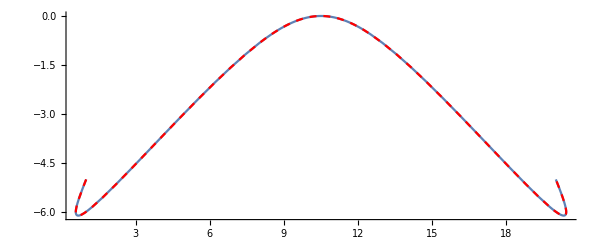

```mathematica
Show[ParametricPlot[{Re[x[t]/.solINI⟦1⟧/.par],Re[eta[t]/.solINI⟦1⟧/.par]},{t,0,1}],
ParametricPlot[{Re[x[t]/.solINI⟦2⟧/.par],Re[eta[t]/.solINI⟦2⟧/.par]},{t,0,1},PlotStyle->{Red, Dashed}],ImageSize->600,PlotRange->All]
```

## sqrt action from n-action

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
L=m/(2 n)(-T'[s]^2+X'[s]^2)-(m n)/2;
```

```mathematica
soln=Solve[D[L,n]==0,n]
```

{{n→-√(T'[s]^2-X'[s]^2)},{n→√(T'[s]^2-X'[s]^2)}}

```mathematica
Simplify[L/.soln⟦1⟧]
```

m √(T'[s]^2-X'[s]^2)

## Classical action in de Sitter

```mathematica
a[eta[s]]=-1/(H eta[s]);
L=FullSimplify[m/(2n)a[eta[s]]^2(-eta'[s]^2+x'[s]^2)-(m n)/2]
```

(c1^2 m)/(2 H^2 n)-(m n)/2

```mathematica
S=Integrate[L,{s,0,1}]
```

(c1^2 m)/(2 H^2 n)-(m n)/2

```mathematica
Scl[n_]=(c1^2 m)/(2 H^2 n)-(m n)/2;
```

```mathematica
solN=Solve[D[ Scl[n],n]==0,n]
```

{{n→-(ⅈ c1)/H},{n→(ⅈ c1)/H}}

```mathematica
ⅈ Scl[n]/.solN⟦1⟧(*/.solINI⟦1⟧*)
ⅈ Scl[n]/.solN⟦2⟧(*/.solINI⟦1⟧*)
```

-(c1 m)/H

(c1 m)/H

```mathematica
ArcTan[∞]
```

π/2

```mathematica
par={EA->-5,EB->-5,XA->1,XB->12,H->0.1,m->1};
```

```mathematica
solN/.solINI⟦1⟧/.par//N
solN/.solINI⟦2⟧/.par//N
```

{{n→-8.87137-31.4159 ⅈ},{n→8.87137+31.4159 ⅈ}}

{{n→8.87137-31.4159 ⅈ},{n→-8.87137+31.4159 ⅈ}}

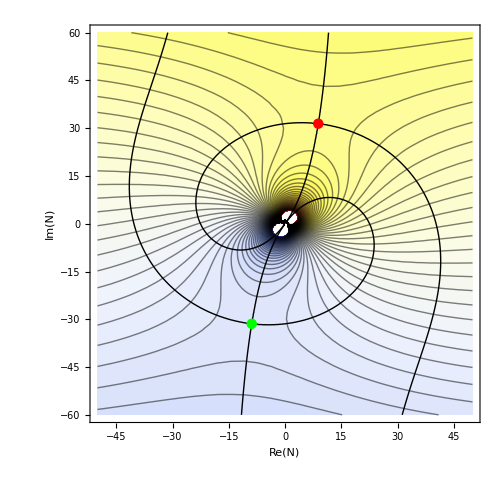

```mathematica
texStyle={FontSize->14,FontColor->Black};
par={EA->-5,EB->-5,XA->1,XB->12,H->0.1,m->1};
Show[ContourPlot[Re[ⅈ Scl[n]/.solINI⟦1⟧//.par/.n->u+ⅈ v],{u,-50,50},{v,-60,60},Contours->80,ColorFunction->"TemperatureMap",c],
ContourPlot[Im[ⅈ Scl[n]/.solINI⟦1⟧//.par/.n->u+ⅈ v]=={Im[ⅈ Scl[n]/.solN⟦2⟧/.solINI⟦1⟧//.par],
Im[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧//.par]},{u,-50,50},{v,-60,60},PlotPoints->50,Axes->True,AxesStyle->Black,ContourStyle->{{Black,Thick},{Black,Thick}}],Graphics[{PointSize[0.015],Red,Point[{Re[n/.solN⟦2⟧/.solINI⟦1⟧//.par],Im[n/.solN⟦2⟧/.solINI⟦1⟧//.par]}]}],Graphics[{PointSize[0.015],Green,Point[{Re[n/.solN⟦1⟧/.solINI⟦1⟧//.par],Im[n/.solN⟦1⟧/.solINI⟦1⟧//.par]}]}],Axes->True,ImageSize->500]
```

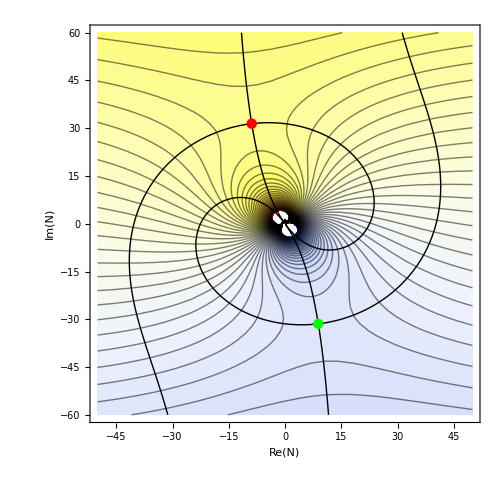

```mathematica
texStyle={FontSize->14,FontColor->Black};
par={EA->-5,EB->-5,XA->1,XB->12,H->0.1,m->1};
Show[ContourPlot[Re[ⅈ Scl[n]/.solINI⟦2⟧//.par/.n->u+ⅈ v],{u,-50,50},{v,-60,60},Contours->80,ColorFunction->"TemperatureMap",Frame-> True, AxesLabel->{"Re(N)","Im(N)"},Axes->True,LabelStyle->texStyle],
ContourPlot[Im[ⅈ Scl[n]/.solINI⟦2⟧//.par/.n->u+ⅈ v]=={Im[ⅈ Scl[n]/.solN⟦2⟧/.solINI⟦2⟧//.par],
Im[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦2⟧//.par]},{u,-50,50},{v,-60,60},PlotPoints->50,Axes->True,AxesStyle->Black,ContourStyle->{{Black,Thick},{Black,Thick}}],Graphics[{PointSize[0.015],Red,Point[{Re[n/.solN⟦2⟧/.solINI⟦2⟧//.par],Im[n/.solN⟦2⟧/.solINI⟦2⟧//.par]}]}],Graphics[{PointSize[0.015],Green,Point[{Re[n/.solN⟦1⟧/.solINI⟦2⟧//.par],Im[n/.solN⟦1⟧/.solINI⟦2⟧//.par]}]}],Axes->True,ImageSize->500]
```

```mathematica
ParametricPlot3D[{Re[ x[s]/.solN⟦1⟧/.solINI⟦1⟧//.par],Re[ eta[s]/.solN⟦1⟧/.solINI⟦1⟧//.par],Im[ eta[s]/.solN⟦1⟧/.solINI⟦1⟧//.par]},{s,0,1},AxesLabel->{"Re(x)","Re(η)","Im(η)"},LabelStyle->texStyle,ImageSize->400,PlotStyle->{Blue}(*,AspectRatio->Automatic*)]
```

-Graphics3D-

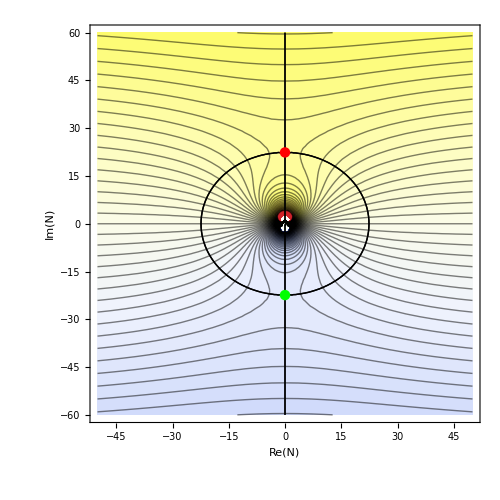

```mathematica
par2={EA->-5,EB->-5,XA->1,XB->10,H->0.1,m->1};
Show[ContourPlot[Re[ⅈ Scl[n]/.solINI⟦1⟧//.par2/.n->u+ⅈ v],{u,-50,50},{v,-60,60},Contours->80,ColorFunction->"TemperatureMap",Frame-> True, AxesLabel->{"Re(N)","Im(N)"},Axes->True,LabelStyle->texStyle],
ContourPlot[Im[ⅈ Scl[n]/.solINI⟦1⟧//.par2/.n->u+ⅈ v]=={Im[ⅈ Scl[n]/.solN⟦2⟧/.solINI⟦1⟧//.par2],
Im[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧//.par2]},{u,-50,50},{v,-60,60},PlotPoints->50,Axes->True,AxesStyle->Black,ContourStyle->{{Black,Thick},{Black,Thick}}],Graphics[{PointSize[0.015],Red,Point[{Re[n/.solN⟦2⟧/.solINI⟦1⟧//.par2],Im[n/.solN⟦2⟧/.solINI⟦1⟧//.par2]}]}],Graphics[{PointSize[0.015],Green,Point[{Re[n/.solN⟦1⟧/.solINI⟦1⟧//.par2],Im[n/.solN⟦1⟧/.solINI⟦1⟧//.par2]}]}],Axes->True,ImageSize->500]
```

```mathematica
ParametricPlot3D[{Re[ x[s]/.solN⟦1⟧/.solINI⟦1⟧//.par2],Re[ eta[s]/.solN⟦1⟧/.solINI⟦1⟧//.par2],Im[ eta[s]/.solN⟦1⟧/.solINI⟦1⟧//.par2]},{s,0,1},AxesLabel->{"Re(x)","Re(η)","Im(η)"},LabelStyle->texStyle,ImageSize->500,PlotStyle->{Blue}(*,AspectRatio->Automatic*)]
```

-Graphics3D-

```mathematica
Simplify[ⅇ^(ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧)/.{EB->EA+Δη,XB->XA+Δx}]
```

ⅇ^(1/4 ⅈ √H m ((√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2)))/Δx)^(3/2) √ArcTan[EA^2-Δx^2+(EA+Δη)^2,√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2))] √((2 √(EA^2 Δx^2) (-Δx^2+Δη (2 EA+Δη)))/((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2))+Log[Cos[1/2 ArcTan[-√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2)),Δx^2-Δη (2 EA+Δη)]]-Sin[1/2 ArcTan[-√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2)),Δx^2-Δη (2 EA+Δη)]]]-Log[Cos[1/2 ArcTan[-√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2)),Δx^2-Δη (2 EA+Δη)]]+Sin[1/2 ArcTan[-√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2)),Δx^2-Δη (2 EA+Δη)]]]-Log[Cos[1/2 (ArcTan[-√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2)),Δx^2-Δη (2 EA+Δη)]+ArcTan[EA^2-Δx^2+(EA+Δη)^2,√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2))])]-Sin[1/2 (ArcTan[-√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2)),Δx^2-Δη (2 EA+Δη)]+ArcTan[EA^2-Δx^2+(EA+Δη)^2,√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2))])]]+Log[Cos[1/2 (ArcTan[-√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2)),Δx^2-Δη (2 EA+Δη)]+ArcTan[EA^2-Δx^2+(EA+Δη)^2,√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2))])]+Sin[1/2 (ArcTan[-√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2)),Δx^2-Δη (2 EA+Δη)]+ArcTan[EA^2-Δx^2+(EA+Δη)^2,√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2))])]]+Sec[ArcTan[-√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2)),Δx^2-Δη (2 EA+Δη)]+ArcTan[EA^2-Δx^2+(EA+Δη)^2,√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2))]] Tan[ArcTan[-√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2)),Δx^2-Δη (2 EA+Δη)]+ArcTan[EA^2-Δx^2+(EA+Δη)^2,√((Δx^2-Δη^2) (4 EA^2-Δx^2+4 EA Δη+Δη^2))]]))

```mathematica
eta[0]
eta[1]
```

c4 Sec[c2]

c4 Sec[c1+c2]

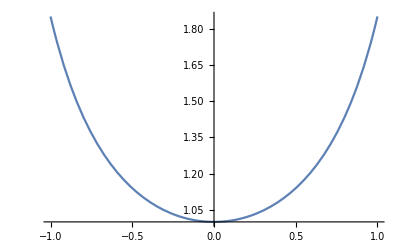

```mathematica
Plot[Sec[x],{x,-1,1}]
```

```mathematica
solconstΔ=Solve[{eta[0]==-1,eta[1]==Δη-1,x[0]==0,x[1]==Δx},{c1,c2,c3,c4}](*/.{C[1]->0,C[2]->0}*)//Simplify
```

{{c3→(Δx^2-(-2+Δη) Δη)/(2 Δx),c4→-(√(-Δx^4-(-2+Δη)^2 Δη^2+2 Δx^2 (2-2 Δη+Δη^2)))/(2 Δx),c1→ConditionalExpression[ArcTan[(-2+Δx^2+2 Δη-Δη^2)/(-1+Δη),(√(-Δx^4-(-2+Δη)^2 Δη^2+2 Δx^2 (2-2 Δη+Δη^2)))/(-1+Δη)]+2 π C[2],C[2]∈Integers],c2→ConditionalExpression[ArcTan[(√(-Δx^4-(-2+Δη)^2 Δη^2+2 Δx^2 (2-2 Δη+Δη^2)))/Δx,(Δx^2-(-2+Δη) Δη)/Δx]+2 π C[1],C[1]∈Integers]},{c3→(Δx^2-(-2+Δη) Δη)/(2 Δx),c4→(√(-Δx^4-(-2+Δη)^2 Δη^2+2 Δx^2 (2-2 Δη+Δη^2)))/(2 Δx),c1→ConditionalExpression[ArcTan[(-2+Δx^2+2 Δη-Δη^2)/(-1+Δη),-(√(-Δx^4-(-2+Δη)^2 Δη^2+2 Δx^2 (2-2 Δη+Δη^2)))/(-1+Δη)]+2 π C[2],C[2]∈Integers],c2→ConditionalExpression[ArcTan[-(√(-Δx^4-(-2+Δη)^2 Δη^2+2 Δx^2 (2-2 Δη+Δη^2)))/Δx,(Δx^2-(-2+Δη) Δη)/Δx]+2 π C[1],C[1]∈Integers]}}

```mathematica
solINIΔ=Simplify[solconstΔ(*,Δx>0*)]
```

{}